```mathematica
TODO:  what is the volume that is excited at different frequencies?  What is the max?
```

for r_s="0.0025", d_xy="0.04763", d_z="0.060006" (all in m)

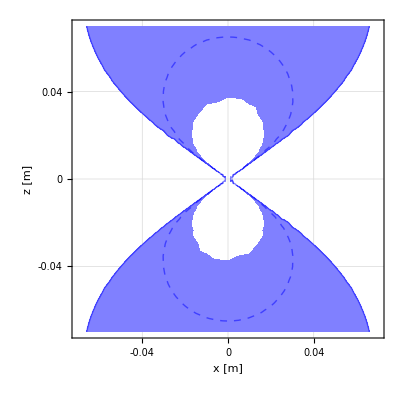

```mathematica
μ0=4π 10^-7;
Msat=  1.36 10^6; (* steel in 3T*)
r1 = 0.0025; (*mm radius sphere*)
m1 = {0,4/3 π r1^3 Msat}; (*magnetization of first dipole*)
m2 =  {0,4/3 π r1^3 Msat};  (*magnetization of second dipole*)
rg =.07;
(*dz = 0.125;
dxy = 0.098;*)

γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = 1500;(*offset*)
BW = 2500;
StringForm["for r_s=``, d_xy=``, d_z=`` (all in m)",NumberForm[r1,4],NumberForm[dxy,4],NumberForm[dz,5]]

ContourPlot[-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2)), { x,-rg,rg},{ z,-rg,rg},Contours->{(Freq-BW/2)/γ,(Freq)/γ,(Freq+BW/2)/γ},ContourStyle->{Blue,Directive[Blue,Dashed],Blue,Red,Directive[Red,Dashed],Red},ContourShading->{None,Lighter[Blue,0.5],Lighter[Blue,0.5],None,Lighter[Red,0.8],Lighter[Red,0.8],None},FrameLabel-> {"x [m]","z [m]"},FrameTicks->{{-0.04,0,0.04},{-0.04,0,0.04},{},{}},PerformanceGoal->"Quality",FrameTicksStyle->Directive[16],LabelStyle->Directive[18],GridLines->Automatic,AspectRatio->1]
```

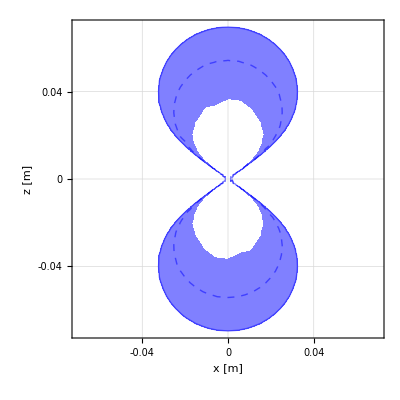

### Draw regions illuminated by dipole’s magnetic region. Assume r1 = [0,0,0]; Todo: use lots of points, save in a cool file format, color negative in one color and positive in the other, show how overlap happens

```mathematica
3500 Hz, Mag 
gamma = 42480000 Hz/T  (42.48 MHz)
F = gamma*B

What is magnetic saturation?
```

```mathematica
N[3500/42480000]
Do contours of 3500 pm 2500/2
```

0.0000823917

```mathematica
μ0=4π 10^-7;
Msat=  1.36 10^6; (* steel in 3T*)
r1 = 0.0025; (*mm radius sphere*)
m1 = {0,0,4/3 π r1^3 Msat}; (*magnetization of first dipole*)
m2 =  {0,0,4/3 π r1^3 Msat};  (*magnetization of second dipole*)
rg =.06;
γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = 3500;
BW = 2500;
BField[r2_] := μ0/(4π)(3 r2/Norm[r2]((r2/Norm[r2]).m1)-m1)/Norm[r2]^3;
RegionPlot3D[r2 = {x,y,z};BField[r2]⟦3⟧>Freq/γ, { x,-rg,rg},{ y,-rg,rg},{ z,-rg,rg}]
```

-Graphics3D-

```mathematica
BB =Graphics3D[{Gray,Sphere[{0,0,0},r1]}];
```

```mathematica
negPlot =RegionPlot3D[r2 = {x,y,z};BField[r2][[3]]>Freq/γ, { x,-rg,rg},{ y,-rg,rg},{ z,-rg,rg},PlotStyle->{Directive[Red,Opacity[0.5]]},Mesh->None, PlotPoints->50,AxesLabel->{"x [m]","y [m]","z [m]"},ViewPoint-> {0.9,-π,1.1},ViewVertical->{0.8,0.5,-0.09},TicksStyle->Directive[16],LabelStyle->Directive[18]];
Show[negPlot,BB]
```

-Graphics3D-

```mathematica
posPlot =RegionPlot3D[r2 = {x,y,z};BField[r2]⟦3⟧<-Freq/γ, { x,-rg,rg},{ y,-rg,rg},{ z,-rg,rg},PlotStyle->{Directive[Blue,Opacity[0.8]]},Mesh->None, PlotPoints->50,AxesLabel->{"x [m]","y [m]","z [m]"},
ViewPoint-> {0.9,-π,1.1},ViewVertical->{0.8,0.5,-0.09},TicksStyle->Directive[16],LabelStyle->Directive[18]];
Show[ posPlot,BB]
```

-Graphics3D-

```mathematica
Show[negPlot, posPlot,BB]
```

-Graphics3D-

```mathematica
-Graphics3D-//Options
```

{AutomaticImageSize→True,Axes→True,AxesLabel→{x,y,z},BoxRatios→{1,1,1},ImageSize→{355.865,342.521},PlotRange→{{-0.12,0.12},{-0.12,0.12},{-0.12,0.12}},PlotRangePadding→{Scaled[0.02],Scaled[0.02],Scaled[0.02]},ViewPoint→,ViewVertical→{0.844545,0.508386,-0.168188}}

### Draw 2D contours illuminated by dipole’s magnetic region. Assume r1 = [0,0,0]; Todo: use lots of points, save in a cool file format, color negative in one color and positive in the other, show how overlap happens

```mathematica
Clear[y]
√(x^2+y^2)
```

√(x^2+y^2)

```mathematica
N[2^(1/3)]
```

1.25992

```mathematica
r1 = 0.005; (*mm radius sphere*)
γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = {1500,2500};(*offset*)

dxy = r1((Msat  μ0 γ)/(3 Freq))^(1/3);
dz =r1 ((2Msat  μ0 γ)/(3 Freq))^(1/3);
StringForm["for r_s=``, d_xy=``, d_z=`` (all in m), Freq_offset = ``Hz",NumberForm[r1,4],NumberForm[dxy,4],NumberForm[dz,5],NumberForm[Freq,5]]
```

for r_s="0.005", d_xy={"0.1263", "0.1066"}, d_z={"0.15918", "0.13426"} (all in m), Freq_offset = {"1500", "2500"}Hz

for r_s="0.0025", d_xy="0.04763", d_z="0.060006" (all in m)

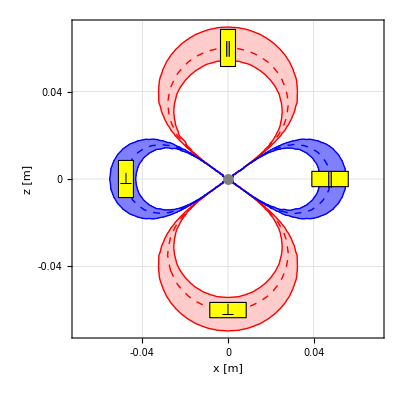

```mathematica
μ0=4π 10^-7;
Msat=  1.36 10^6; (* steel in 3T*)
r1 = 0.0025; (*mm radius sphere*)
m1 = {0,4/3 π r1^3 Msat}; (*magnetization of first dipole*)
m2 =  {0,4/3 π r1^3 Msat};  (*magnetization of second dipole*)
rg =.07;
(*dz = 0.125;
dxy = 0.098;*)

γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = 3500;(*offset*)
BW = 2500;
dxy = r1((Msat  μ0 γ)/(3 Freq))^(1/3);
dz =r1 ((2Msat  μ0 γ)/(3 Freq))^(1/3);
StringForm["for r_s=``, d_xy=``, d_z=`` (all in m)",NumberForm[r1,4],NumberForm[dxy,4],NumberForm[dz,5]]

mkRad = 0.0035; (*MR spot radius*)
mkHLength = 0.0085;(*MR-spot half-length*)
BField2D[{x_,y_}] := μ0/(4π)(3{x,y}/(√(x^2+y^2))(({x,y}/(√(x^2+y^2))).m1)-m1)/((√(x^2+y^2))^3);
ContourPlot[-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2)), { x,-rg,rg},{ z,-rg,rg},Contours->{(-(Freq-BW/2))/γ,(-(Freq))/γ,(-(Freq+BW/2))/γ,(Freq-BW/2)/γ,(Freq)/γ,(Freq+BW/2)/γ},ContourStyle->{Blue,Directive[Blue,Dashed],Blue,Red,Directive[Red,Dashed],Red},ContourShading->{None,Lighter[Blue,0.5],Lighter[Blue,0.5],None,Lighter[Red,0.8],Lighter[Red,0.8],None},Epilog->{Gray,Disk[{0,0},r1],
Yellow,EdgeForm[Black],
Rectangle[{-mkRad,dz-mkHLength},{mkRad,dz+mkHLength},RoundingRadius->0.005],
Rectangle[{-mkHLength,-(dz-mkRad)},{mkHLength,-(dz+mkRad)},RoundingRadius->0.005],
Rectangle[{dxy-mkHLength,-mkRad},{dxy+mkHLength,mkRad},RoundingRadius->0.005],
Rectangle[{-(dxy-mkRad),-mkHLength},{-(dxy+ mkRad),mkHLength},RoundingRadius->0.005],
Black,
Text[Style["⊥",16],{0,-dz}],
Text[Style["∥",16],{0,+dz}],
Text[Style["⊥",16],{-dxy,0}],
Text[Style["∥",16],{dxy,0}]
},FrameLabel-> {"x [m]","z [m]"},FrameTicks->{{-0.04,0,0.04},{-0.04,0,0.04},{},{}},PerformanceGoal->"Quality",FrameTicksStyle->Directive[16],LabelStyle->Directive[18],GridLines->Automatic,AspectRatio->1]
```

High Quality Publication version

```mathematica
rg =.075;
contourDensityPlot[-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2)), { x,-rg,rg},{ z,-rg,rg},
Contours->{(-(Freq-BW/2))/γ,(-(Freq))/γ,(-(Freq+BW/2))/γ,(Freq-BW/2)/γ,(Freq)/γ,(Freq+BW/2)/γ},Frame->True,

ContourStyle->{Blue,Directive[Blue,Dashed],Blue,Red,Directive[Red,Dashed],Red},
ContourShading->{None,Lighter[Blue,0.5],Lighter[Blue,0.5],None,Lighter[Red,0.8],Lighter[Red,0.8],None},
Epilog->{Gray,Disk[{0,0},r1],
Yellow,EdgeForm[Black],
Rectangle[{-mkRad,dz-mkHLength},{mkRad,dz+mkHLength},RoundingRadius->0.005],
Rectangle[{-mkHLength,-(dz-mkRad)},{mkHLength,-(dz+mkRad)},RoundingRadius->0.005],
Rectangle[{dxy-mkHLength,-mkRad},{dxy+mkHLength,mkRad},RoundingRadius->0.005],
Rectangle[{-(dxy-mkRad),-mkHLength},{-(dxy+ mkRad),mkHLength},RoundingRadius->0.005],
Black,
Text[Style["⊥",16],{0,-dz}],
Text[Style["∥",16],{0,+dz}],
Text[Style["⊥",16],{-dxy,0}],
Text[Style["∥",16],{dxy,0}]
},FrameLabel-> {"x [m]","z [m]"},FrameTicks->{{-0.04,0,0.04},{-0.04,0,0.04},{},{}},
PerformanceGoal->"Quality",FrameTicksStyle->Directive[16],LabelStyle->Directive[18],ImageSize-> Medium,"ShadingOpacity"->0.7,GridLines->Automatic,AspectRatio->Automatic,MaxRecursion->5]
```

-Graphics-

#### What is the revolution solid of the maximum magnetic field as it revolves around an axis?

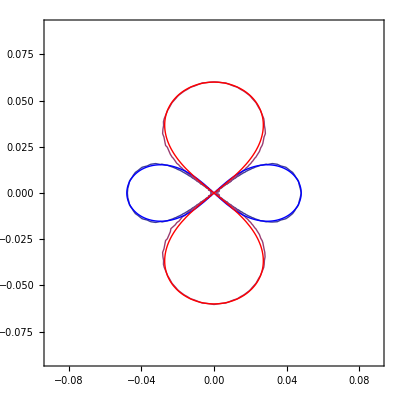

```mathematica
rg = 0.09;
r = 0.04;
cp = ContourPlot[{-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2))==(-(Freq))/γ,-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2))==(Freq)/γ}, { x,-rg,rg},{ z,-rg,rg},PerformanceGoal->"Quality"];
sc = 0.048;
pp1 =ParametricPlot[sc{Cos[t]/(1+Sin[t]^2),.9(Sin[t]Cos[t])/(1+Sin[t]^2)},{t,0,2π},PlotStyle->Blue];
pp2 =ParametricPlot[sc{1.6(Sin[t]Cos[t])/(1+Sin[t]^2),1.25 Cos[t]/(1+Sin[t]^2)},{t,0,2π},PlotStyle->Red];
Show[cp,pp1,pp2]
```

```mathematica
illumRegionb =RevolutionPlot3D[{sc Cos[t]/(1+Sin[t]^2),.9sc(Sin[t]Cos[t])/(1+Sin[t]^2)},{t,0,2π},{θ,0,π},PlotStyle->Directive[Opacity[1],Blue],RevolutionAxis->{0,0,1}];
illumRegiona =RevolutionPlot3D[{1.6sc(Sin[t]Cos[t])/(1+Sin[t]^2),1.25sc Cos[t]/(1+Sin[t]^2)},{t,0,2π},PlotStyle->Directive[Opacity[1],Red]];
```

```mathematica
comb = Graphics3D[Translate[{illumRegiona⟦1⟧,illumRegionb⟦1⟧},{rad,0,0}]];
Show[comb,PlotRange->All]
```

-Graphics3D-

```mathematica
RevolutionPlot3D
```

```mathematica
rad =0.032;
pp13 =RevolutionPlot3D[{rad+sc Cos[t]/(1+Sin[t]^2),.9sc(Sin[t]Cos[t])/(1+Sin[t]^2)} ,{t,0,2π},PlotStyle->Directive[Opacity[0.4],Blue],MeshStyle->Opacity[0.2]]; 
pp23 =RevolutionPlot3D[{rad+1.6sc(Sin[t]Cos[t])/(1+Sin[t]^2),1.25sc Cos[t]/(1+Sin[t]^2)},{t,0,2π},PlotStyle->Directive[Opacity[0.4],Red],MeshStyle->Opacity[0.2]];
```

```mathematica
Show[pp23,pp13,comb,PlotRange->All]
```

-Graphics3D-

### THis one is wrong ... we need the swept out volume, not a rotated volume

```mathematica
illumRegionbT=RevolutionPlot3D[{sc Cos[t]/(1+Sin[t]^2),.9sc(Sin[t]Cos[t])/(1+Sin[t]^2)},{t,0,2π},{θ,0,π},PlotStyle->Directive[Opacity[0.5],Blue],RevolutionAxis->{0,0,1},MeshStyle->Opacity[0.2]];
illumRegionaT =RevolutionPlot3D[{1.6sc(Sin[t]Cos[t])/(1+Sin[t]^2),1.25sc Cos[t]/(1+Sin[t]^2)},{t,0,2π},PlotStyle->Directive[Opacity[0.5],Red],MeshStyle->Opacity[0.2]];
```

```mathematica
comb = Graphics3D[Translate[{illumRegiona⟦1⟧,illumRegionb⟦1⟧},Table[rad{0,Sin[a],Cos[a]},{a,0,(1+3/4)π,π/4}]]];
Show[comb,PlotRange->All]
```

-Graphics3D-

### How close must two spheres be in order to move capsule out of magnetic field?

```mathematica
Clear[ μ0,Msat,r1,Msat,r2,m1]
m1 = {0,0,4/3 π r1^3 Msat}; (*magnetization of first dipole*)
r2 = {x,y,z};
offs = {d1x,0,d1z};
Simplify[(μ0/(4π)(3 r2/Norm[r2]((r2/Norm[r2]).m1)-m1)/Norm[r2]^3)⟦3⟧]
Simplify[(μ0/(4π)(3(r2-offs)/Norm[r2-offs](((r2-offs)/Norm[r2-offs]).m1)-m1)/Norm[r2-offs]^3)⟦3⟧]
```

-(Msat r1^3 μ0 (-3 z^2+Abs[x]^2+Abs[y]^2+Abs[z]^2))/(3 (Abs[x]^2+Abs[y]^2+Abs[z]^2)^(5/2))

-(Msat r1^3 μ0 (-3 d1z^2+6 d1z z-3 z^2+Abs[d1x-x]^2+Abs[y]^2+Abs[d1z-z]^2))/(3 (Abs[d1x-x]^2+Abs[y]^2+Abs[d1z-z]^2)^(5/2))

```mathematica
FullSimplify[-(Msat r1^3 μ0 (-3 d1z^2+6 d1z z-3 z^2+(d1x-x)^2+y^2+(d1z-z)^2))/(3 ((d1x-x)^2+y^2+(d1z-z)^2)^(5/2))]
```

-(Msat r1^3 ((d1x-x)^2+y^2-2 (d1z-z)^2) μ0)/(3 ((d1x-x)^2+y^2+(d1z-z)^2)^(5/2))

```mathematica
FullSimplify[1/3 Msat r1^3 (-(x^2+y^2-2 (d1-z)^2)/((x^2+y^2+(d1-z)^2)^(5/2))-(x^2+y^2-2 z^2)/((x^2+y^2+z^2)^(5/2))) μ0]
```

```mathematica
FullSimplify[-(Msat r1^3 μ0 (-3 z^2+x^2+y^2+z^2))/(3 (x^2+y^2+z^2)^(5/2))-(Msat r1^3 ((d1x-x)^2+y^2-2 (d1z-z)^2) μ0)/(3 ((d1x-x)^2+y^2+(d1z-z)^2)^(5/2))]
```

-(Msat r1^3 ((d1x-x)^2+y^2-2 (d1z-z)^2) μ0)/(3 ((d1x-x)^2+y^2+(d1z-z)^2)^(5/2))-(Msat r1^3 (x^2+y^2-2 z^2) μ0)/(3 (x^2+y^2+z^2)^(5/2))

```mathematica
μ0=4π 10^-7;
Msat=  1.36 10^6; (* steel in 3T*)
r1 = 0.0025; (*mm radius sphere*)
m1 = {0,4/3 π r1^3 Msat}; (*magnetization of first dipole*)
m2 =  {0,4/3 π r1^3 Msat};  (*magnetization of second dipole*)
rg =.07;
(*dz = 0.125;
dxy = 0.098;*)

γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = 3500;
BW = 2500;
dxy = ((Msat r1^3 μ0 γ)/(3 Freq))^(1/3);
dz = ((2Msat r1^3 μ0 γ)/(3 Freq))^(1/3);
mkRad = 0.0035; (*MR spot radius*)
mkHLength = 0.0085;(*MR-spot half-length*)
BField2D[{x_,y_}] := μ0/(4π)(3{x,y}/(√(x^2+y^2))(({x,y}/(√(x^2+y^2))).m1)-m1)/((√(x^2+y^2))^3);
d1xV=0.13373702001739043;
d1zV = 0.174882676967863;
Manipulate[ContourPlot[{(*-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2)),*)-(Msat r1^3 ((d1x-x)^2+y^2-2 (d1z-z)^2) μ0)/(3 ((d1x-x)^2+y^2+(d1z-z)^2)^(5/2))-(Msat r1^3 (x^2+y^2-2 z^2) μ0)/(3 (x^2+y^2+z^2)^(5/2))}/.{y->0}, { x,-2rg,.8rg},{ z,-3rg,rg},Contours->{(-(Freq-BW/2))/γ,(-(Freq))/γ,(-(Freq+BW/2))/γ,(Freq-BW/2)/γ,(Freq)/γ,(Freq+BW/2)/γ},ContourStyle->{Blue,Directive[Blue,Dashed],Blue,Red,Directive[Red,Dashed],Red},ContourShading->{None,Lighter[Blue,0.5],Lighter[Blue,0.5],None,Lighter[Red,0.8],Lighter[Red,0.8],None},
Prolog->{Orange,Opacity[0.25],(* Rectangle[{-d1xV,-d1zV},{d1xV,d1zV}]*),
Polygon[{{-d1xV,0},{0,d1zV},{d1xV,0},{0,-d1zV}}]},
Epilog->{Gray,Disk[{0,0},r1],Disk[{d1x,d1z},r1],
Yellow,EdgeForm[Black],
Rectangle[{-mkHLength,-(dz-mkRad)},{mkHLength,-(dz+mkRad)},RoundingRadius->0.005],
Rectangle[{-(dxy-mkRad),-mkHLength},{-(dxy+ mkRad),mkHLength},RoundingRadius->0.005],
Black,
Text[Style["⊥",16],{0,-dz}],
Text[Style["⊥",16],{-dxy,0}]
},FrameLabel-> {"x [m]","z [m]"},FrameTicks->{Table[Chop[.05 k],{k,-5,5}],Table[Chop[.05 k],{k,-5,5}],{},{}}
,PerformanceGoal->"Quality",MaxRecursion->4,FrameTicksStyle->Directive[16],LabelStyle->Directive[18],GridLines->Automatic,AspectRatio->Automatic],
{d1x,-0.2,0},
{d1z,-0.2,0}
]
```